# Rigid bodies, plastic impact

```mathematica
param={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,mO->3000,r->0.12,γ->0.5};
paramExtraction={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,r->0.12,γ->0.5};
```

```mathematica
θ00=π/2;q10=0;q20=π/3;xb0=4;yb0=2;
```

```mathematica
paramScheme={θ0[t]->θ00,q1[t]->q10,q2[t]->q20,xb[t]->xb0,yb[t]->yb0};
test=2000;
```

## Kinematics

## Manipulator

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | {θ0[t],q1[t],q2[t]}
0 | 0 | 0 | 1)

```mathematica
Mfb=Mrotztrasl[0,{xb[t],yb[t],0}];
```

```mathematica
Mb0=Mrotztrasl[θ0[t],{0,0,0}];
```

```mathematica
Mf0=Mfb.Mb0;Mf0//MatrixForm
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | xb[t]
Sin[θ0[t]] | Cos[θ0[t]] | 0 | yb[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M01=Mrotztrasl[q1[t],{l1 Cos[q1[t]],l1 Sin[q1[t]],0}];M01//MatrixForm
```

(Cos[q1[t]] | -Sin[q1[t]] | 0 | l1 Cos[q1[t]]
Sin[q1[t]] | Cos[q1[t]] | 0 | l1 Sin[q1[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[q2[t],{l2 Cos[q2[t]],l2 Sin[q2[t]],0}];M12//MatrixForm
```

(Cos[q2[t]] | -Sin[q2[t]] | 0 | l2 Cos[q2[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | l2 Sin[q2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02=Simplify[M01.M12];
```

```mathematica
Mf1=Simplify[Mf0.M01];
```

```mathematica
Mf2=Simplify[Mf1.M12];
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
Ob=Mfb.origin;Ob//MatrixForm
```

(xb[t]
yb[t]
0
1)

```mathematica
O1=Mf1.origin;O1//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+yb[t]
0
1)

```mathematica
EE=Simplify[Mf2.origin];EE//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+l2 Sin[q1[t]+q2[t]+θ0[t]]+yb[t]
0
1)

Jacobian matrixOb:

```mathematica
J=FullSimplify[D[EE[[1;;2]],{{xb[t],yb[t],θ0[t],q1[t],q2[t]}}]];J//MatrixForm
```

(1 | 0 | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l2 Sin[q1[t]+q2[t]+θ0[t]]
0 | 1 | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l2 Cos[q1[t]+q2[t]+θ0[t]])

```mathematica
J. D[{xb[t],yb[t],θ0[t],q1[t],q2[t]},t]==D[EE[[1;;2]],t]//Simplify
```

True

### Plot a 2D scheme of the robot

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
labels={"xf","yf"};
```

```mathematica
For[i=1,i<3,i++,u={0,0};(*initializing u as a null 3 elements vector*)u⟦i⟧=1;(*Setting the i-th element of u equal to 1,to have a unit vector*)RF0arrow[i]=Graphics[{Thickness[0.010],Red,Arrowheads[0.04],
Text[labels⟦i⟧,2 u+0.07],Arrow[{{0,0},2 u}]},Axes->True]];
```

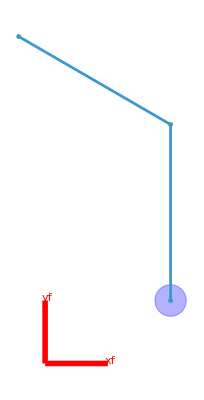

```mathematica
Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],RobotPlot,RF0arrow[1],RF0arrow[2]}]
```

```mathematica
paraml={l1->2.0,l2->3.0};
```

```mathematica
Manipulate[Show[{ListLinePlot[{Ob[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},O1[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},EE[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5}}/.paraml,PlotRange->{{-5,8},{-5,8}},AspectRatio->1,PlotMarkers->{Automatic, 5}]},Block[{r=0.5},Graphics[{EdgeForm[Thick],Blue,Opacity[0.3],Disk[Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},r],Thickness[0.007],Opacity[0.5],Red,Arrowheads[0.04],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 /.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1/.paraml/.paramScheme}}],Blue,Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]-l1 Sin[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Cos[a3]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 Cos[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Sin[a3]/.paraml/.paramScheme}}]}]],RF0arrow[1],RF0arrow[2]],{a1,0,3},{a2,0,3},{a3,0,π/4},{a4,0,π/4},{a5,0,π/4}]
```

## Object

-Graphics-

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: xb, yOb, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocityOb of the dof and the contact point:

```mathematica
MfO0=Mrotztrasl[0,{xO[t],yO[t],0}];MfO0//MatrixForm
```

(1 | 0 | 0 | xO[t]
0 | 1 | 0 | yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO0O1=Mrotztrasl[Ω[t],{0,0,0}];MO0O1//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO1O2=Mrotztrasl[γ,{r Cos[γ] ,r Sin[γ],0}];MO1O2//MatrixForm
```

(Cos[γ] | -Sin[γ] | 0 | r Cos[γ]
Sin[γ] | Cos[γ] | 0 | r Sin[γ]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MfO1=MfO0.MO0O1;
MfO2=Simplify[MfO0.MO0O1.MO1O2];MfO2//MatrixForm
```

(Cos[γ+Ω[t]] | -Sin[γ+Ω[t]] | 0 | r Cos[γ+Ω[t]]+xO[t]
Sin[γ+Ω[t]] | Cos[γ+Ω[t]] | 0 | r Sin[γ+Ω[t]]+yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactP=(MfO2.{0,0,0,1})[[1;;2]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

(r Cos[γ+Ω[t]]+xO[t]
r Sin[γ+Ω[t]]+yO[t])

(xO'[t]-r Sin[γ+Ω[t]] Ω'[t]
yO'[t]+r Cos[γ+Ω[t]] Ω'[t])

```mathematica
Jo=D[contactP,{{xO[t],yO[t],Ω[t]}}];Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

```mathematica
Transpose[Jo]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[γ+Ω[t]] | r Cos[γ+Ω[t]])

```mathematica
Jo.ψ'==velContactP//Simplify
```

True

## Dynamics

## Manipulator

### IR method

The mass is considered distributed, hence the pseudo inertia tensor can be written like this:

```mathematica
Ixb=1/4 mb r^2;
Iyb=1/4 mb r^2;
Izb=0;
Ix1=1/3m1 l1^2;
Ix2=1/3 m2 l2^2;
```

Inertia frame in the com of the round base:

```mathematica
J00={{Ixb,0,0,0},{0,Iyb,0,0},{0,0,Izb,0},{0,0,0,mb}};J00//MatrixForm
```

((mb r^2)/4 | 0 | 0 | 0
0 | (mb r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J0f=Simplify[Mf0.J00.Transpose[Mf0]];J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
J11={{Ix1,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J11//MatrixForm
```

((l1^2 m1)/3 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J1f=Simplify[Mf1.J11.Transpose[Mf1]];
```

```mathematica
J22={{Ix2,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J22//MatrixForm
```

((l2^2 m2)/3 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J2f=Simplify[Mf2.J22.Transpose[Mf2]];
```

```mathematica
Wf0=Simplify[D[Mf0,t].Inverse[Mf0]];Wf0//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb=Simplify[D[Mfb,t].Inverse[Mfb]];Wfb//MatrixForm
```

(0 | 0 | 0 | xb'[t]
0 | 0 | 0 | yb'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0=Simplify[D[Mb0,t].Inverse[Mb0]];Wb0//MatrixForm
```

(0 | -θ0'[t] | 0 | 0
θ0'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0Ff=Simplify[Mfb.Wb0.Inverse[Mfb]];Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | yb[t] θ0'[t]
θ0'[t] | 0 | 0 | -xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb+Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Lfbx=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Lfby=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Lb0=Wb0/θ0'[t];
```

```mathematica
Lb0Ff=Simplify[Mf0.Lb0.Inverse[Mf0]];Lb0Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -q1'[t] | 0 | 0
q1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01=W01/q1'[t];
```

```mathematica
L01Ff=Simplify[Mf0.L01.Inverse[Mf0]];L01Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf1=Simplify[D[Mf1,t].Inverse[Mf1]];Wf1//MatrixForm
```

(0 | -q1'[t]-θ0'[t] | 0 | xb'[t]+yb[t] (q1'[t]+θ0'[t])
q1'[t]+θ0'[t] | 0 | 0 | yb'[t]-xb[t] (q1'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12=Simplify[D[M12,t].Inverse[M12]];W12//MatrixForm
```

(0 | -q2'[t] | 0 | 0
q2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L12=W12/q2'[t];
L12Ff=Simplify[Mf1.L12.Inverse[Mf1]];L12Ff//MatrixForm
```

(0 | -1 | 0 | l1 Sin[q1[t]+θ0[t]]+yb[t]
1 | 0 | 0 | -l1 Cos[q1[t]+θ0[t]]-xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf2=Simplify[D[Mf2,t].Inverse[Mf2]];Wf2//MatrixForm
```

(0 | -q1'[t]-q2'[t]-θ0'[t] | 0 | l1 Sin[q1[t]+θ0[t]] q2'[t]+xb'[t]+yb[t] (q1'[t]+q2'[t]+θ0'[t])
q1'[t]+q2'[t]+θ0'[t] | 0 | 0 | -l1 Cos[q1[t]+θ0[t]] q2'[t]+yb'[t]-xb[t] (q1'[t]+q2'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
T1=Simplify[1/2Tr[Wf0.J0f.Transpose[Wf0]]];
T2=Simplify[1/2Tr[Wf1.J1f.Transpose[Wf1]]];
T3=Simplify[1/2Tr[Wf2.J2f.Transpose[Wf2]]];
```

The potential energy of body i, denoted by Ui, consists of two parts; one due to the gravity gradient and the other due to the elastic strain energy stored in the flexbible body. The effect of the former is much smaller than the latter and is neglected here. Hence the potential energy of a rigid body is equal to zero.

```mathematica
L=T1+T2+T3;
```

ByOb neglecting the constraints forces (since theyOb don’t affect the lagrange equation), we get the actions matrices:

```mathematica
actionMatrix[cx_,cy_,cz_,fx_,fy_,fz_]:={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
```

```mathematica
ϕ0b=actionMatrix[0,0,τ1-τ2,Fx,Fy,0];ϕ0b//MatrixForm
```

(0 | -τ1+τ2 | 0 | Fx
τ1-τ2 | 0 | 0 | Fy
0 | 0 | 0 | 0
-Fx | -Fy | 0 | 0)

```mathematica
ϕbf=FullSimplify[Mf0.ϕ0b.Transpose[Mf0]];
```

```mathematica
ϕ11=actionMatrix[0,0,τ2-τ3,0,0,0];ϕ11//MatrixForm
ϕ1f=FullSimplify[Mf1.ϕ11.Transpose[Mf1]];ϕ1f//MatrixForm
```

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ϕ22=actionMatrix[0,0,τ3,0,0,0];
ϕ2f=FullSimplify[Mf2.ϕ22.Transpose[Mf2]];
```

Let’s derivate the non-lagrangian components:

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]];
```

```mathematica
f1=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfbx]]
f2=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfby]]
f3=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lb0Ff]]
f4=FullSimplify[PSS[(ϕ1f+ϕ2f),L01Ff]]
f5=Simplify[PSS[(ϕ2f),L12Ff]]
```

Fx Cos[θ0[t]]-Fy Sin[θ0[t]]

Fy Cos[θ0[t]]+Fx Sin[θ0[t]]

τ1

τ2

τ3

```mathematica
eq1=Simplify[D[D[L,xb'[t]],t]-D[L,xb[t]]-f1];
eq2=Simplify[D[D[L,yb'[t]],t]-D[L,yb[t]]-f2];
eq3=Simplify[D[D[L,θ0'[t]],t]-D[L,θ0[t]]-f3];
eq4=Simplify[D[D[L,q1'[t]],t]-D[L,q1[t]]-f4];
eq5=Simplify[D[D[L,q2'[t]],t]-D[L,q2[t]]-f5];
```

```mathematica
{c,A}=FullSimplify[Normal@CoefficientArrays[{eq1,eq2,eq3,eq4,eq5},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M=A[[1;;5,1;;5]];
u=-A[[1;;5,6;;10]];
```

```mathematica
MatrixForm[M]
```

(m1+m2+mb | 0 | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | -1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]]
0 | m1+m2+mb | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]]
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/6 (2 l2^2 m2+2 l1^2 (m1+3 m2)+3 mb r^2+6 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
-1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]] | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]] | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | (l2^2 m2)/3)

```mathematica
MatrixForm[u]
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | 0 | 0
Sin[θ0[t]] | Cos[θ0[t]] | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[c]
```

(1/2 (-l1 (m1+2 m2) Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Cos[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2+l2 m2 Sin[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q1[t]+θ0[t]] Sin[q2[t]] (q1'[t]+q2'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
1/2 l1 l2 m2 Sin[q2[t]] (q1'[t]+θ0'[t])^2)

Equation of motion: Mp^(..)+ c = u

### Classic Lagrangian method

```mathematica
Ob2D=(Mfb.{0,0,0,1})[[1;;2]];
O12D=(Mf1.{-l1/2,0,0,1})[[1;;2]]
EE2D=(Mf2.{-l2/2,0,0,1})[[1;;2]];
```

{1/2 l1 Cos[q1[t]+θ0[t]]+xb[t],1/2 l1 Sin[q1[t]+θ0[t]]+yb[t]}

```mathematica
vb=D[Ob2D,t]
v1=D[O12D,t]
v2=D[EE2D,t]
```

{xb'[t],yb'[t]}

{xb'[t]-1/2 l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t]),yb'[t]+1/2 l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])}

{xb'[t]-l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-1/2 l2 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]),yb'[t]+l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])+1/2 l2 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])}

```mathematica
vbsquare=Simplify[vb[[1]]^2+vb[[2]]^2];
v1square=Simplify[v1[[1]]^2+v1[[2]]^2];
v2square=Simplify[v2[[1]]^2+v2[[2]]^2];
```

Inertia wrt CoM:

```mathematica
Ib=1/2mb r^2;
I1=1/12m1 l1^2;
I2=1/12m2 l2^2;
```

```mathematica
tb=1/2mb vbsquare+1/2Ib θ0'[t]^2;
t1=1/2m1 v1square+1/2I1 (θ0'[t]+q1'[t])^2;
t2=1/2m2 v2square+1/2I2 (θ0'[t]+q1'[t]+q2'[t])^2;
```

```mathematica
lmid=tb+t1+t2;
```

```mathematica
eq1Mid=Simplify[D[D[lmid,xb'[t]],t]-D[lmid,xb[t]]-f1];
eq2Mid=Simplify[D[D[lmid,yb'[t]],t]-D[lmid,yb[t]]-f2];
eq3Mid=Simplify[D[D[lmid,θ0'[t]],t]-D[lmid,θ0[t]]-f3];
eq4Mid=Simplify[D[D[lmid,q1'[t]],t]-D[lmid,q1[t]]-f4];
eq5Mid=Simplify[D[D[lmid,q2'[t]],t]-D[lmid,q2[t]]-f5];
```

```mathematica
{c2,A2}=FullSimplify[Normal@CoefficientArrays[{eq1Mid,eq2Mid,eq3Mid,eq4Mid,eq5Mid},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M2=A2[[1;;5,1;;5]];
u2=-A2[[1;;5,6;;10]];
```

```mathematica
FullSimplify[c2-c]
```

{0,0,0,0,0}

```mathematica
FullSimplify[M[[1]]==M2[[1]]]
FullSimplify[M[[2]]==M2[[2]]]
FullSimplify[M[[3]]==M2[[3]]]
FullSimplify[M[[4]]==M2[[4]]]
FullSimplify[M[[5]]==M2[[5]]]
```

True

True

True

«2 more identical outputs»

## Object

### IR method

```mathematica
IxO=1/4 mO r^2;
IyO=1/4 mO r^2;
IzO=0;
```

```mathematica
JO1O1={{IxO,0,0,0},{0,IyO,0,0},{0,0,IzO,0},{0,0,0,mO}};JO1O1//MatrixForm
```

((mO r^2)/4 | 0 | 0 | 0
0 | (mO r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mO)

```mathematica
J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
JOf=Simplify[MfO1.JO1O1.Transpose[MfO1]];JOf//MatrixForm
```

(1/4 mO (r^2+4 xO[t]^2) | mO xO[t] yO[t] | 0 | mO xO[t]
mO xO[t] yO[t] | 1/4 mO (r^2+4 yO[t]^2) | 0 | mO yO[t]
0 | 0 | 0 | 0
mO xO[t] | mO yO[t] | 0 | mO)

```mathematica
WfO1=Simplify[D[MfO1,t].Inverse[MfO1]];WfO1//MatrixForm
```

(0 | -Ω'[t] | 0 | xO'[t]+yO[t] Ω'[t]
Ω'[t] | 0 | 0 | yO'[t]-xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1=Simplify[D[MO0O1,t].Inverse[MO0O1]];WO0O1//MatrixForm
```

(0 | -Ω'[t] | 0 | 0
Ω'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1Ff=FullSimplify[MfO0.WO0O1.Inverse[MfO0]];WO0O1Ff//MatrixForm
```

(0 | -Ω'[t] | 0 | yO[t] Ω'[t]
Ω'[t] | 0 | 0 | -xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LO0O1Ff=Simplify[WO0O1Ff/Ω'[t]];LO0O1Ff//MatrixForm
```

(0 | -1 | 0 | yO[t]
1 | 0 | 0 | -xO[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LfOx=Lfbx;
LfOy=Lfby;
```

```mathematica
ϕO1O1=actionMatrix[0,0,τO,FOx,FOy,0];
ϕO1O1Ff=FullSimplify[MfO1.ϕO1O1.Transpose[MfO1]];
```

```mathematica
f1O=FullSimplify[PSS[ϕO1O1Ff,LfOx]]
f2O=FullSimplify[PSS[ϕO1O1Ff,LfOy]]
f3O=FullSimplify[PSS[ϕO1O1Ff,LO0O1Ff]]
```

FOx Cos[Ω[t]]-FOy Sin[Ω[t]]

FOy Cos[Ω[t]]+FOx Sin[Ω[t]]

τO

```mathematica
TO=Simplify[1/2Tr[WfO1.JOf.Transpose[WfO1]]];
LO=TO;
```

```mathematica
eq1OIR=Simplify[D[D[LO,xO'[t]],t]-D[L,xO[t]]-f1O];
eq2OIR=Simplify[D[D[LO,yO'[t]],t]-D[L,yO[t]]-f2O];
eq3OIR=Simplify[D[D[LO,Ω'[t]],t]-D[L,Ω[t]]-f3O];
```

```mathematica
{co,Ao}=FullSimplify[Normal@CoefficientArrays[{eq1OIR,eq2OIR,eq3OIR},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}]];
Mo=Ao[[1;;3,1;;3]];
uo=-Ao[[1;;3,4;;6]];
```

```mathematica
Mo//MatrixForm
co//MatrixForm
uo//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

### Classic method

```mathematica
Iz=1/2mO r^2;
```

```mathematica
T=1/2 mO(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2;
```

```mathematica
eq1O=Simplify[D[D[T,xO'[t]],t]-D[T,xO[t]]-f1O];
eq2O=Simplify[D[D[T,yO'[t]],t]-D[T,yO[t]]-f2O];
eq3O=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-f3O];
```

```mathematica
{co2,Ao2}=Normal@CoefficientArrays[{eq1O,eq2O,eq3O},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}];
Mo2=Ao2[[1;;3,1;;3]];
uo2=-Ao2[[1;;3,4;;6]];
```

```mathematica
Mo2//MatrixForm
co2//MatrixForm
uo2//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

-Graphics-

```mathematica
Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

In the 2007 paper, there is an error when calculating the pseudo-inverse. The correct is the following:

```mathematica
pseudoInverseJo=Transpose[Jo].Inverse[Jo.Transpose[Jo]]//Simplify;pseudoInverseJo//MatrixForm
```

((2+r^2+r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2)) | (r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2)
(r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2) | (2+r^2-r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2))
-(r Sin[γ+Ω[t]])/(1+r^2) | (r Cos[γ+Ω[t]])/(1+r^2))

```mathematica
G=M+Transpose[J].Transpose[pseudoInverseJo].Mo.pseudoInverseJo.J//FullSimplify ;
```

```mathematica
p={xb[t],yb[t],θ0[t],q1[t],q2[t]};
p'=D[p,t];
```

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

```mathematica
H=M. p'+Transpose[J].Transpose[pseudoInverseJo].Mo.ψ'//Simplify;
```

Final values of the general coordinated of the base+manipulator after the impact:

```mathematica
Transpose[J[[1;;2]]/.param/.paramScheme]//MatrixForm
```

(1 | 0
0 | 1
-8.385 | -4.84108
-8.385 | -4.84108
-2.795 | -4.84108)

```mathematica
Chop[Inverse[G]/.param/.paramScheme/.Ω[t]->contactCondition]//MatrixForm
```

(2.38195×10^-6 | -1.5105×10^-10 | 0 | 4.34331×10^-7 | -4.38485×10^-7
-1.5105×10^-10 | 2.3799×10^-6 | 0 | -2.26913×10^-7 | 7.17152×10^-7
0 | 0 | 0.000330904 | -0.000330904 | 0
4.34331×10^-7 | -2.26913×10^-7 | -0.000330904 | 0.000343334 | -0.0000186688
-4.38485×10^-7 | 7.17152×10^-7 | 0 | -0.0000186688 | 0.0000387107)

```mathematica
pf'=Inverse[G].H ;
```

Final values of the satellite after the impact:

```mathematica
ψf'=pseudoInverseJo.J.pf';
```

### Initial conditions

After the capture, we assume that the object is now perfectlyOb attached to the EE, hence the contact point’s variables coincides with the ones of the EE. We also assume that the spinning velocityOb is resetted:

```mathematica
EEi=EE[[1;;2]]/.param/.paramScheme
```

{-0.841082,10.385}

Condition for alignment of the object with the EE:

```mathematica
contactCondition=(θ00+q10+q20+π-(γ/.param))
```

5.25959

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.103923+xO[t],-0.06+yO[t]}

```mathematica
objectPosI=(Solve[{EEi[[1]]==(contactP/.param/.Ω[t]->contactCondition)[[1]],EEi[[2]]==(contactP/.param/.Ω[t]->contactCondition)[[2]]},{xO[t],yO[t]}])[[1]]
```

{xO[t]→-0.945005,yO[t]→10.445}

Let’s suppose initial zero velocities of the BM system.

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/3,xb[t]→4,yb[t]→2}

```mathematica
initialConditions1={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->1,yO'[t]->0,Ω'[t]->0.01};
initialConditions2={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->0,yO'[t]->-1,Ω'[t]->0.01};
```

```mathematica
pf1'=pf'/.initialConditions1/.param/.paramScheme//Chop
pf2'=pf'/.initialConditions2/.param/.paramScheme//Chop
```

{-0.000102493,-0.000302925,0,-0.153968,0.144454}

{-0.0000604807,-0.0000222822,0,-0.0908562,0.288955}

```mathematica
ψf1'=ψf'/.initialConditions1/.param/.paramScheme//Chop
ψf2'=ψf'/.initialConditions2/.param/.paramScheme//Chop
```

{0.88374,0.0398139,0.057162}

{-0.0398025,-0.948542,-0.100964}

```mathematica
a=((Jo.ψf')/.initialConditions1/.param/.paramScheme)
```

{0.88717,0.0457543}

```mathematica
b=((J.pf')/.initialConditions1/.param/.paramScheme)
```

{0.88717,0.0457543}

```mathematica
a-b//Chop
```

{0,0}

## Post-impact

-Graphics-

```mathematica
EEp=EE[[1;;2]]/.param;
```

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.103923+xO[t],-0.06+yO[t]}

```mathematica
contactConditionP=(θ0[t]+q1[t]+q2[t]+π-(γ/.param));
```

```mathematica
objectPosP=(Solve[{EE[[1]]==(contactP/.param/.Ω[t]->contactConditionP)[[1]],EE[[2]]==(contactP/.param/.Ω[t]->contactConditionP)[[2]]},{xO[t],yO[t]}])[[1]];
```

```mathematica
ψp={objectPosP[[1,2]],objectPosP[[2,2]],contactConditionP};
```

We can now write the Jacobian matrix of the object as a function of the EE:

```mathematica
EEsubst={ψ[[1]]->ψp[[1]],ψ[[2]]->ψp[[2]],ψ[[3]]->ψp[[3]]}
```

{xO[t]→-1. (-l1 Cos[q1[t]+θ0[t]]-l2 Cos[q1[t]+q2[t]+θ0[t]]+0.12 Cos[3.14159+q1[t]+q2[t]+θ0[t]]-xb[t]),yO[t]→-1. (-l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]]+0.12 Sin[3.14159+q1[t]+q2[t]+θ0[t]]-yb[t]),Ω[t]→2.64159+q1[t]+q2[t]+θ0[t]}

```mathematica
Jop=Jo/.EEsubst;
```

```mathematica
pseudoInverseJop=Transpose[Jop].Inverse[Jop.Transpose[Jop]]//Simplify;
```

Since we are considering only rigid bodies, there is no contribution of the elastic part (no matrix K).

```mathematica
Mp=M+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.J;
```

```mathematica
Cp=c+Transpose[J].Transpose[pseudoInverseJop].Mo.D[pseudoInverseJop,t].J.p'+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.D[J,t].p'+Transpose[J].Transpose[pseudoInverseJop].co;
```

```mathematica
eqMotion=Mp.D[p,t,t]+Cp;
```

```mathematica
Dimensions[eqMotion]
```

{5}

```mathematica
Mp/.param
```

### Simulation with no control

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/3,xb[t]→4,yb[t]→2}

```mathematica
NDinitialCondition1={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf1'[[1]],yb'[0]==pf1'[[2]],θ0'[0]==pf1'[[3]],q1'[0]==pf1'[[4]],q2'[0]==pf1'[[5]]}
NDinitialCondition2={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf2'[[1]],yb'[0]==pf2'[[2]],θ0'[0]==pf2'[[3]],q1'[0]==pf2'[[4]],q2'[0]==pf2'[[5]]}
```

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/3,xb'[0]==-0.000102493,yb'[0]==-0.000302925,θ0'[0]==0,q1'[0]==-0.153968,q2'[0]==0.144454}

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/3,xb'[0]==-0.0000604807,yb'[0]==-0.0000222822,θ0'[0]==0,q1'[0]==-0.0908562,q2'[0]==0.288955}

```mathematica
solMotion1=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotion2=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

```mathematica
imgSize=475;
imagePadding={{100,10},{25,10}};
```

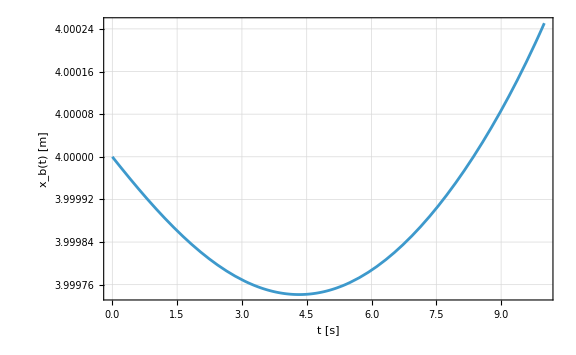
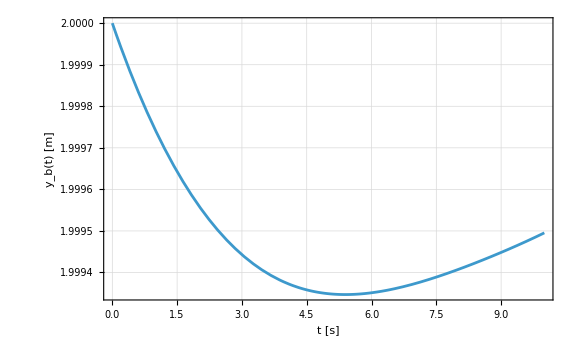
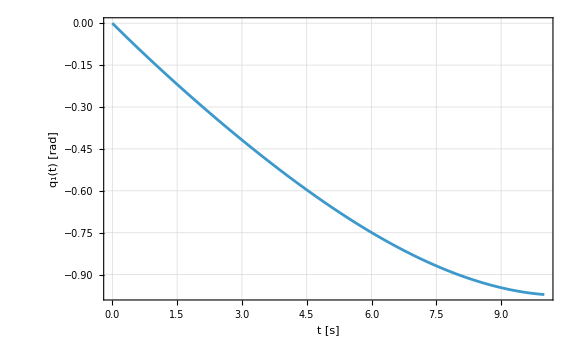
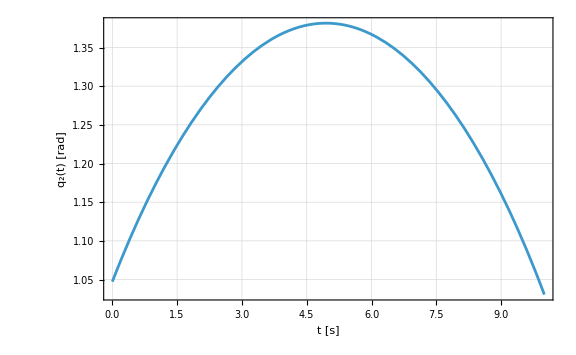
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotion1[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

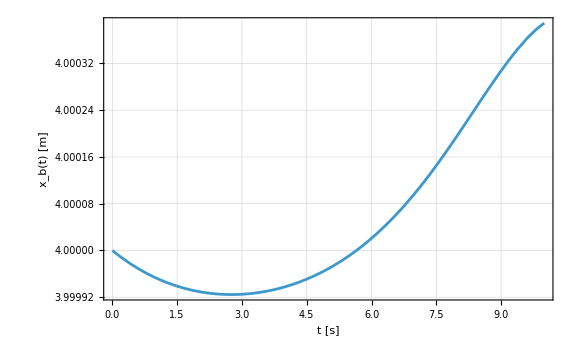
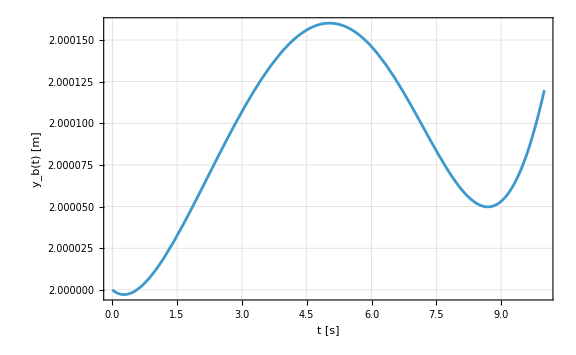
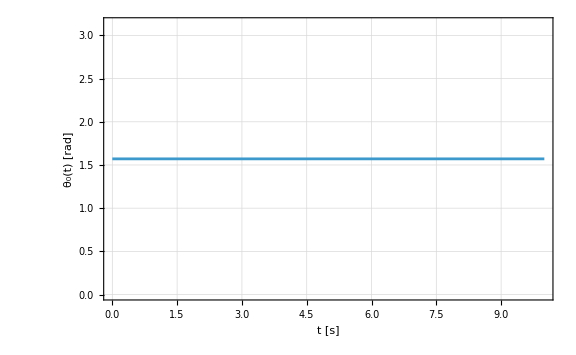
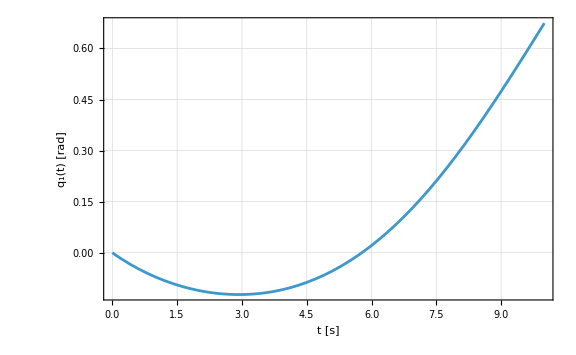
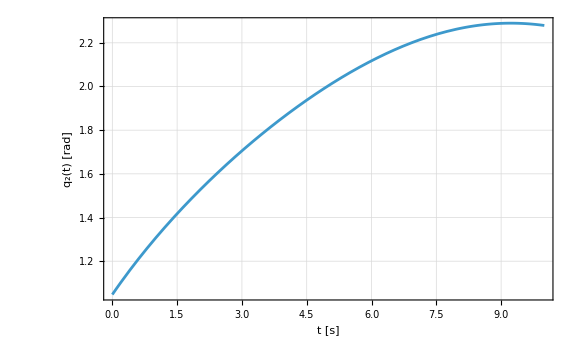

```mathematica
Row[{Plot[solMotion2[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10}
{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10}
```

{{4.00025,1.9995},{8.61508,5.15409},{8.28338,10.7342}}

{{4.00039,2.00012},{0.510317,6.36676},{-0.533639,0.875102}}

```mathematica
RobotPlotAfter1=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
RobotPlotAfter2=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

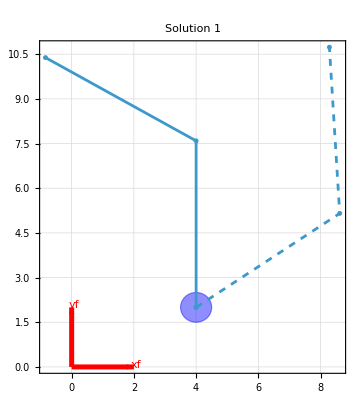
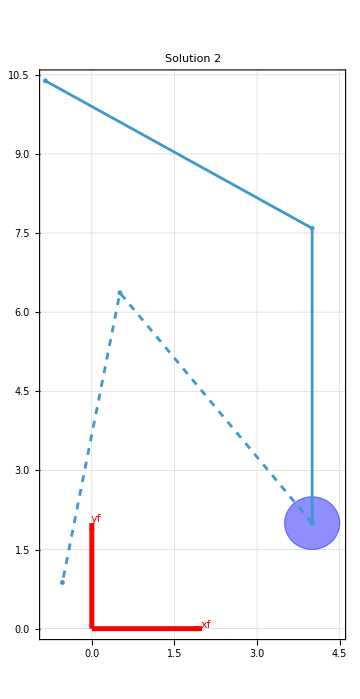

```mathematica
Row[{Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->10,r]}]],RobotPlot,RobotPlotAfter1,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 1",ImageSize->Medium],Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion2/.t->10,r]}]],RobotPlot,RobotPlotAfter2,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 2",ImageSize->Medium]}]
```

### Simulation with control

Let’s suppose a critical damped behaviour (i.e. ξ=1):

```mathematica
Kp=1IdentityMatrix[3];
Kv0=2 Sqrt[Kp];
Kv1=2 0.5 Sqrt[Kp];
Kv2=2 1.5 Sqrt[Kp];
```

```mathematica
pd={θ0[t],q1[t],q2[t]}/.paramScheme
pd'={0,0,0};
```

{π/2,0,π/3}

```mathematica
p3={θ0[t],q1[t],q2[t]};
p3'=D[p3,t];
```

```mathematica
Mtt=Mp[[1;;2,1;;2]];
Mtr=Mp[[1;;2,3;;5]];
Mrt=Mp[[3;;5,1;;2]];
Mrr=Mp[[3;;5,3;;5]];
Ct=Cp[[1;;2]];
Cr=Cp[[3;;5]];
```

```mathematica
Mhat=Mrr-Mrt.Inverse[Mtt].Mtr;
Chat=Cr-Mrt.Inverse[Mtt].Ct;
```

```mathematica
U0=-Mhat.(Kv0.(p3'-pd')+Kp.(p3-pd))+Chat;
U1=-Mhat.(Kv1.(p3'-pd')+Kp.(p3-pd))+Chat;
U2=-Mhat.(Kv2.(p3'-pd')+Kp.(p3-pd))+Chat;
```

```mathematica
eqMotionControl10=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl20=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl30=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U0[[1]];
eqMotionControl40=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U0[[2]];
eqMotionControl50=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U0[[3]];
```

```mathematica
eqMotionControl11=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl21=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl31=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U1[[1]];
eqMotionControl41=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U1[[2]];
eqMotionControl51=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U1[[3]];
```

```mathematica
eqMotionControl12=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl22=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl32=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U2[[1]];
eqMotionControl42=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U2[[2]];
eqMotionControl52=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U2[[3]];
```

```mathematica
solMotionControl10=NDSolve[{(eqMotionControl10/.param)==0,(eqMotionControl20/.param)==0,(eqMotionControl30/.param)==0,(eqMotionControl40/.param)==0,(eqMotionControl50/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl20=NDSolve[{(eqMotionControl10/.param)==0,(eqMotionControl20/.param)==0,(eqMotionControl30/.param)==0,(eqMotionControl40/.param)==0,(eqMotionControl50/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl11=NDSolve[{(eqMotionControl11/.param)==0,(eqMotionControl21/.param)==0,(eqMotionControl31/.param)==0,(eqMotionControl41/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl21=NDSolve[{(eqMotionControl11/.param)==0,(eqMotionControl21/.param)==0,(eqMotionControl31/.param)==0,(eqMotionControl41/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl12=NDSolve[{(eqMotionControl12/.param)==0,(eqMotionControl22/.param)==0,(eqMotionControl32/.param)==0,(eqMotionControl42/.param)==0,(eqMotionControl52/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl22=NDSolve[{(eqMotionControl12/.param)==0,(eqMotionControl22/.param)==0,(eqMotionControl32/.param)==0,(eqMotionControl42/.param)==0,(eqMotionControl52/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

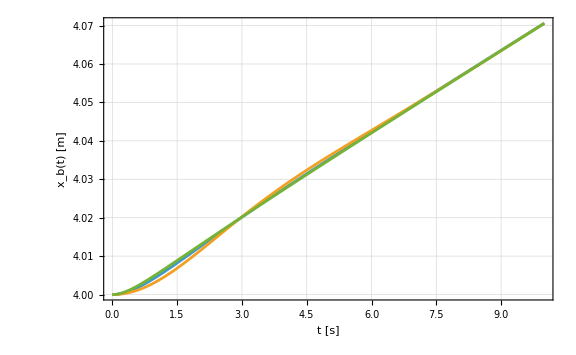
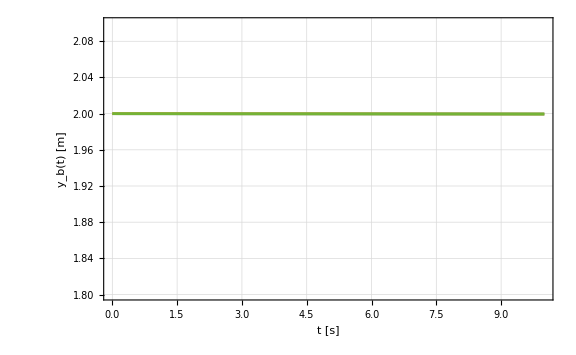
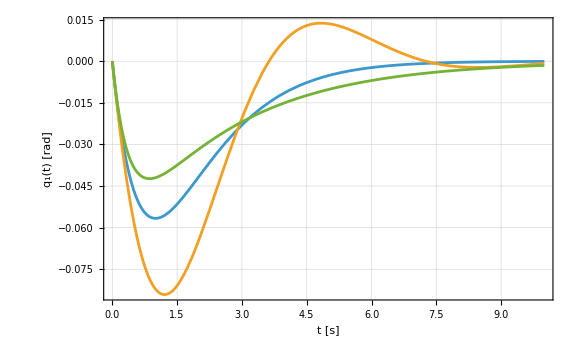
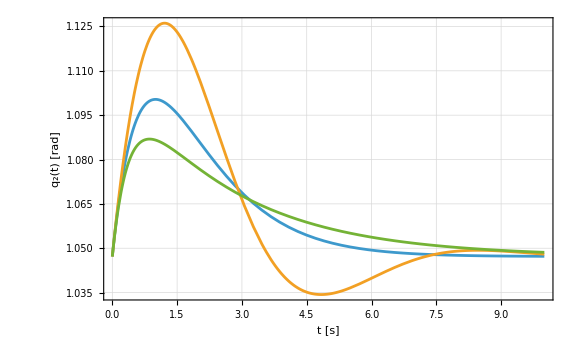
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[{solMotionControl10[[1,2]],solMotionControl11[[1,2]],solMotionControl12[[1,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl10[[2,2]],solMotionControl11[[2,2]],solMotionControl12[[2,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}},ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl10[[3,2]],solMotionControl11[[3,2]],solMotionControl12[[3,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl10[[4,2]],solMotionControl11[[4,2]],solMotionControl12[[4,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl10[[5,2]],solMotionControl11[[5,2]],solMotionControl12[[5,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

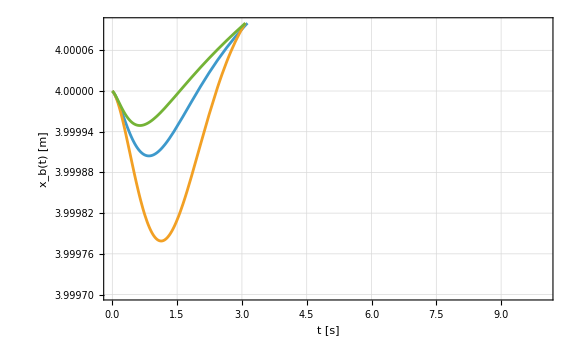
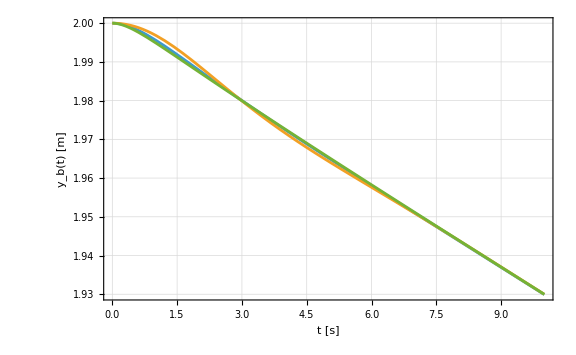
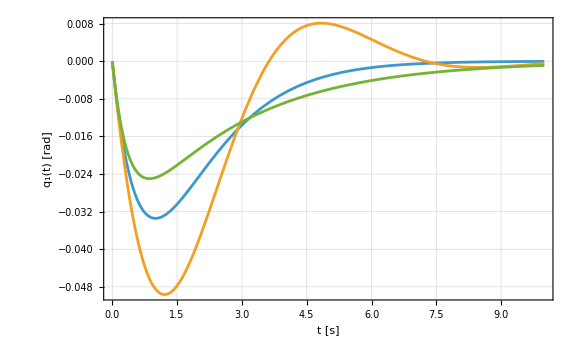
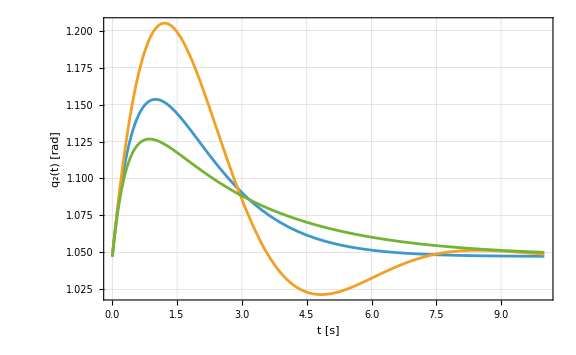
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[{solMotionControl20[[1,2]],solMotionControl21[[1,2]],solMotionControl22[[1,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{3.9997,4.0001}},ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[2,2]],solMotionControl21[[2,2]],solMotionControl22[[2,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[3,2]],solMotionControl21[[3,2]],solMotionControl22[[3,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[4,2]],solMotionControl21[[4,2]],solMotionControl22[[4,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[5,2]],solMotionControl21[[5,2]],solMotionControl22[[5,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

### Simulation with uknown mass

```mathematica
series[f_,v_,v0_,order_]:=Module[{e},Expand[Normal[Series[f/.Thread[v->v0+e*v],{e,0,order}]]/.e->1]]
```

```mathematica
Kp=1IdentityMatrix[2];
Kv0=1.999*Sqrt[Kp];
```

```mathematica
pd0={q100,q200};
```

```mathematica
eqMotionStim4=series[(Mp[[4,1;;5]].D[p,t,t]+Cp[[4]])/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,θ0[t]->π/2,θ0'[t]->0},{q1[t],q2[t],q1'[t],q2'[t],q1''[t],q2''[t]},{q100,q200,0,0,0,0},1];
eqMotionStim5=series[(Mp[[5,1;;5]].D[p,t,t]+Cp[[5]])/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,θ0[t]->π/2,θ0'[t]->0},{q1[t],q2[t],q1'[t],q2'[t],q1''[t],q2''[t]},{q100,q200,0,0,0,0},1];
```

```mathematica
{c,Mlin}=Normal@CoefficientArrays[{eqMotionStim4,eqMotionStim5},{q1''[t],q2''[t]}];
```

```mathematica
Ulin=-(Mlin/.mO->test).(Kv0.(p'[[4;;5]]-pd'[[2;;3]])+Kp.(p[[4;;5]]-pd0));
```

```mathematica
linearizedEq1Real=((eqMotionStim4/.paramExtraction)-Ulin[[1]])//Simplify;
linearizedEq2Real=((eqMotionStim5/.paramExtraction)-Ulin[[2]])//Simplify;
```

```mathematica
linearSol1=Simplify@Chop@DSolve[{(linearizedEq1Real/.q100->q10/.q200->q20/.mO->3000)==0,(linearizedEq2Real/.q100->q10/.q200->q20/.mO->3000)==0,q1[0]==q10,q1'[0]==pf1'[[4]],q2[0]==q20,q2'[0]==pf1'[[5]]},{q1[t],q2[t]},t][[1]];
linearSol2=Simplify@Chop@DSolve[{(linearizedEq1Real/.q100->q10/.q200->q20/.mO->3000)==0,(linearizedEq2Real/.q100->q10/.q200->q20/.mO->3000)==0,q1[0]==q10,q1'[0]==pf2'[[4]],q2[0]==q20,q2'[0]==pf2'[[5]]},{q1[t],q2[t]},t][[1]];
```

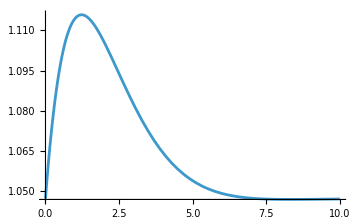
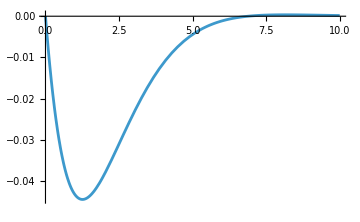

```mathematica
Row[{Plot[{q2[t]/.linearSol1},{t,0,10},PlotRange->{{0,10},All},ImageSize->Medium],Plot[{q1[t]/.linearSol2},{t,0,10},PlotRange->{{0,10},All},ImageSize->Medium]}]
```

```mathematica
Mpstim=Mp/.mO->test;
Cpstim=Cp/.mO->test;
```

```mathematica
Kp=1IdentityMatrix[3];
Kv=2 Sqrt[Kp];
```

```mathematica
Mttstim=Mpstim[[1;;2,1;;2]];
Mtrstim=Mpstim[[1;;2,3;;5]];
Mrtstim=Mpstim[[3;;5,1;;2]];
Mrrstim=Mpstim[[3;;5,3;;5]];
Ctstim=Cpstim[[1;;2]];
Crstim=Cpstim[[3;;5]];
```

```mathematica
Mhatstim=Mrrstim-Mrtstim.Inverse[Mttstim].Mtrstim;
Chatstim=Crstim-Mrtstim.Inverse[Mttstim].Ctstim;
```

```mathematica
U=-Mhatstim.(Kv.(p3'-pd')+Kp.(p3-pd))+Chatstim;
```

```mathematica
eqMotionControlStim1=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControlStim2=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControlStim3=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U[[1]];
eqMotionControlStim4=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U[[2]];
eqMotionControlStim5=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U[[3]];
```

```mathematica
solMotionControl1=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15}, Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl2=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15}, Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl1Data=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition1},{xb,yb,θ0,q1,q2},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl2Data=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition2},{xb,yb,θ0,q1,q2},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]];
```

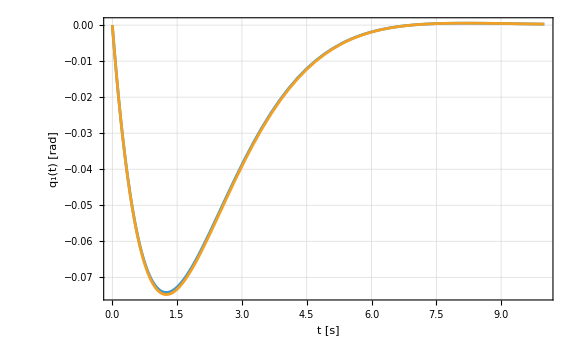

```mathematica
Plot[{solMotionControl1[[4,2]],q1[t]/.linearSol1},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

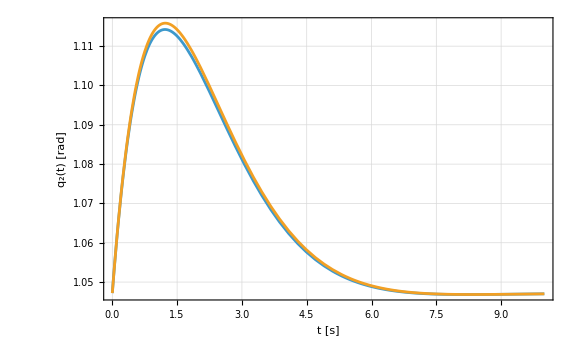

```mathematica
Plot[{solMotionControl1[[5,2]],q2[t]/.linearSol1},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

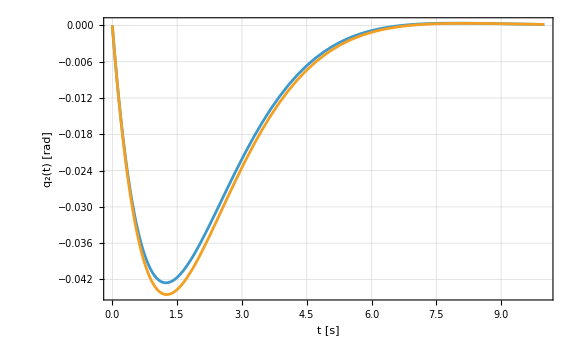

```mathematica
Plot[{solMotionControl2[[4,2]],q1[t]/.linearSol2},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

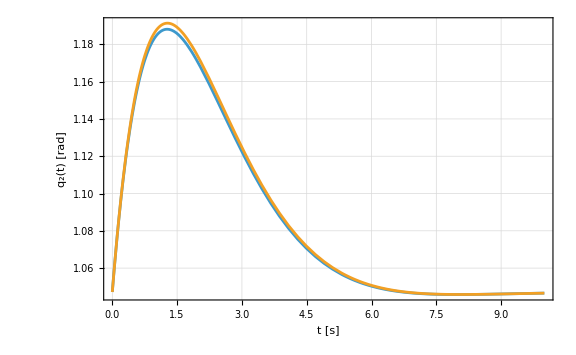

```mathematica
Plot[{solMotionControl2[[5,2]],q2[t]/.linearSol2},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

```mathematica
linearizedEq1Real/.q100->q10/.q200->0//Simplify
linearizedEq2Real/.q100->q10/.q200->q20//Simplify
```

-101138.+203850. q1[t]+96579.5 q2[t]+407496. q1'[t]+193063. q2'[t]+20311.3 q1''[t]+91.7694 mO q1''[t]+5468.42 q2''[t]+45.5556 mO q2''[t]

-66879.9+96579.5 q1[t]+63865.6 q2[t]+193063. q1'[t]+127667. q2'[t]+5468.42 q1''[t]+45.5556 mO q1''[t]+3124.81 q2''[t]+30.3704 mO q2''[t]

```mathematica
eqApprox1=linearizedEq1Real/.q100->q10/.q200->q20/.q2[t]->q20/.q2'[t]->0/.q2''[t]->0//Simplify
eqApprox2=linearizedEq2Real/.q100->q10/.q200->q20/.q1[t]->q10/.q1'[t]->0/.q1''[t]->0//Simplify
```

0.+203850. q1[t]+407496. q1'[t]+20311.3 q1''[t]+91.7694 mO q1''[t]

-66879.9+63865.6 q2[t]+127667. q2'[t]+3124.81 q2''[t]+30.3704 mO q2''[t]

```mathematica
q2App=Simplify[DSolve[{(linearizedEq2Real/.q100->q10/.q200->q20/.q1[t]->q10/.q1'[t]->0/.q1''[t]->0)==0,q2[0]==q20,q2'[0]==pf1'[[5]]},q2[t],t][[1]]]
q1App=DSolve[{(linearizedEq1Real/.q100->q10/.q200->q20/.q2[t]->q20/.q2'[t]->0/.q2''[t]->0)==0,q1[0]==q10,q1'[0]==pf1'[[4]]},q1[t],t][[1]]
```

{q2[t]→1.0472+(ⅇ^(((-2101.84-45.8573 √(1997.9-1. mO)) t)/(102.89+1. mO)) (-0.162056-0.00157504 mO))/(√(1997.9-1. mO))+(ⅇ^(((-2101.84+45.8573 √(1997.9-1. mO)) t)/(102.89+1. mO)) (0.162056+0.00157504 mO))/(√(1997.9-1. mO))}

{q1[t]→1/(√(1997.78-1. mO))0.00163341 (221.329 ⅇ^(1/2 (-4440.44/(221.329+1. mO)-(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t)-221.329 ⅇ^(1/2 (-4440.44/(221.329+1. mO)+(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t)+1. ⅇ^(1/2 (-4440.44/(221.329+1. mO)-(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t) mO-1. ⅇ^(1/2 (-4440.44/(221.329+1. mO)+(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t) mO)}

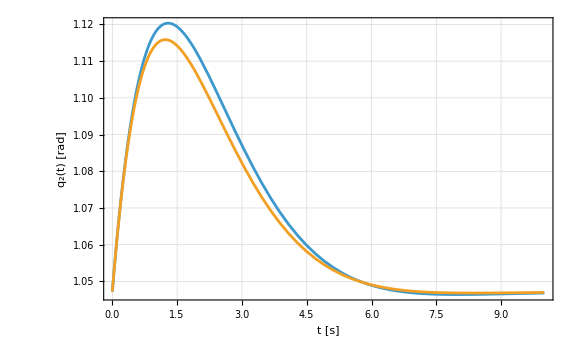

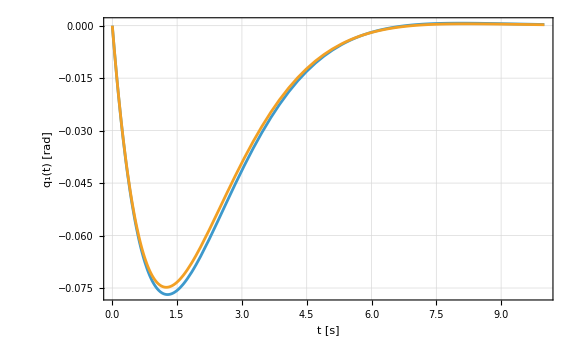

```mathematica
Plot[{q2[t]/.q2App/.mO->3000,q2[t]/.linearSol1},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
Plot[{q1[t]/.q1App/.mO->3000,q1[t]/.linearSol1},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

#### Nonlinearfit Symbolic Form

```mathematica
q11Data=Transpose@{solMotionControl1Data[[4,2,3]][[1]],solMotionControl1Data[[4,2,4,3,1;;Dimensions[solMotionControl1Data[[4,2,4,3]]][[1]];;3]]};
q21Data=Transpose@{solMotionControl1Data[[5,2,3]][[1]],solMotionControl1Data[[5,2,4,3,1;;Dimensions[solMotionControl1Data[[5,2,4,3]]][[1]];;3]]};
q12Data=Transpose@{solMotionControl2Data[[4,2,3]][[1]],solMotionControl2Data[[4,2,4,3,1;;Dimensions[solMotionControl2Data[[4,2,4,3]]][[1]];;3]]};
q22Data=Transpose@{solMotionControl2Data[[5,2,3]][[1]],solMotionControl2Data[[5,2,4,3,1;;Dimensions[solMotionControl2Data[[5,2,4,3]]][[1]];;3]]};
```

```mathematica
sol11=DSolve[{eqApprox1==0,q1[0]==q10,q1'[0]==pf1'[[4]]},q1[t],t][[1]];
sol21=DSolve[{eqApprox2==0,q2[0]==q20,q2'[0]==pf1'[[5]]},q2[t],t][[1]];
sol12=DSolve[{eqApprox1==0,q1[0]==q10,q1'[0]==pf2'[[4]]},q1[t],t][[1]];
sol22=DSolve[{eqApprox2==0,q2[0]==q20,q2'[0]==pf2'[[5]]},q2[t],t][[1]];
```

```mathematica
table1=Table[Plot[q1[t]/.sol11/.mO->300*i,{t,0,10},PlotRange->{Automatic,All},PlotStyle->ColorData[i+77,"ColorFunction"],PlotLegends->Placed[LineLegend[{Row[{"m = ",300*i," kg"}]}],{1,0.5}],Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],{i,1,15}];
Show[table1]
```

-Graphics-

```mathematica
errorFunction[q_,data_]:=NIntegrate[(q-data)^2,{t,0,10}];
```

```mathematica
q11DataNoise=Interpolation[Transpose@{q11Data[[All,1]],q11Data[[All,2]]+noiseData1y}];
```

Thread::tdlen: Objects of unequal length in {0.,-0.0000153946,-0.0000307869,-0.0000615663,-0.000123097,-0.000184594,-0.000307481,-0.000430225,-0.000675285,-0.00116369,-0.00164982,-0.00213368,«27»,-0.0688239,-0.0700598,-0.0711142,-0.0719972,-0.0727184,-0.0732871,-0.0737122,-0.0740023,-0.0741654,-0.0742095,-0.0741421,«82»}+{«1»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.,0.0001,0.0002,0.0004,0.0008,0.0012,0.002,0.0028,0.0044,0.0076,0.0108,0.014,0.0172,0.0236,0.03,0.0364,0.0492,0.062,0.0748,«13»,0.51512,0.5612,0.60728,0.65336,0.69944,0.74552,0.7916,0.83768,0.88376,0.92984,0.97592,1.022,1.06808,1.11416,1.16024,1.20632,1.2524,1.29848,«82»},{«1»}+«1»} cannot be transposed.

Interpolation::innd: First argument in («1»)^T does not contain a list of data and coordinates.

```mathematica
realmass11=FindMinimum[errorFunction[(q1[t]/.sol11),q11DataNoise[t]],{mO,test},Method->"PrincipalAxis"][[2,1,2]]//Timing
```

NIntegrate::inumr: The integrand ((0.00163341 (221.329 ⅇ^(1/2 Plus[«2»] t)-221.329 ⅇ^(«1»)+1. ⅇ^(«1») mO-1. ⅇ^(1/2 Plus[«2»] t) mO))/(√(1997.78-1. mO))-Interpolation[{{0.,«49»,«82»},{«132»}+{«148»}}^T][t])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

NIntegrate::inumr: The integrand ((0.-0.00109608 ⅈ) (2221.33 ⅇ^((-0.9995-0.0316188 ⅈ) t)-2221.33 ⅇ^((-0.9995+0.0316188 ⅈ) t))-Interpolation[{{0.,0.0001,«48»,«82»},«1»}^T][t])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::nrnum: The function value NIntegrate[((0.00163341 (221.329 Compile`$14-221.329 Compile`$19+1. «11» mO-1. Compile`$19 mO))/(√(Compile`$3))-Interpolation[{][t])^2,{t,0,10}] is not a real number at {mO} = {2000.}.

Part::partd: Part specification FindMinimum[errorFunction[q1[t]/.sol11,q11DataNoise[t]],{mO,test},Method→PrincipalAxis]⟦2,1,2⟧ is longer than depth of object.

FindMinimum::nrnum: The function value NIntegrate[((0.00163341 (221.329 Compile`$14-221.329 Compile`$19+1. «11» mO-1. Compile`$19 mO))/(√(Compile`$3))-Interpolation[{][t])^2,{t,0,10}] is not a real number at {mO} = {2000.}.

Part::partd: Part specification FindMinimum[errorFunction[q1[t]/.sol11,q11DataNoise[t]],{mO,test},Method→PrincipalAxis]⟦2,1,2⟧ is longer than depth of object.

FindMinimum::nrnum: The function value NIntegrate[((0.00163341 (221.329 Compile`$14-221.329 Compile`$19+1. «11» mO-1. Compile`$19 mO))/(√(Compile`$3))-Interpolation[{][t])^2,{t,0,10}] is not a real number at {mO} = {2000.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

Part::partd: Part specification FindMinimum[errorFunction[q1[t]/.sol11,q11DataNoise[t]],{mO,test},Method→PrincipalAxis]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{0.0341,FindMinimum[errorFunction[q1[t]/.sol11,q11DataNoise[t]],{mO,test},Method→PrincipalAxis]⟦2,1,2⟧}

```mathematica
q1[t]/.sol11
```

1/(√(1997.78-1. mO))0.00163341 (221.329 ⅇ^(1/2 (-4440.44/(221.329+1. mO)-(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t)-221.329 ⅇ^(1/2 (-4440.44/(221.329+1. mO)+(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t)+1. ⅇ^(1/2 (-4440.44/(221.329+1. mO)-(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t) mO-1. ⅇ^(1/2 (-4440.44/(221.329+1. mO)+(94.262 √(1997.78-1. mO))/(221.329+1. mO)) t) mO)

```mathematica
nlmq11Symb=NonlinearModelFit[q11Data,q1[t]/.sol11,{{mO,1997}},t]
nlmq11Symb["ParameterTable"]
real11Symbolic=nlmq11Symb["ParameterTableEntries"][[1,1]]
```

NonlinearModelFit::nrlnum: The function value {0.+0. ⅈ,-1.1272×10^-9+0. ⅈ,-2.26722×10^-9+0. ⅈ,-3.12221×10^-9+0. ⅈ,-5.86899×10^-9+0. ⅈ,-7.22345×10^-9+0. ⅈ,-9.94159×10^-9+0. ⅈ,-1.2742×10^-8+0. ⅈ,-2.03728×10^-8+0. ⅈ,«33»,0.000184561+0. ⅈ,0.000207909+0. ⅈ,0.000231625+0. ⅈ,0.000255548+0. ⅈ,0.000279526+0. ⅈ,0.000303414+0. ⅈ,0.000327074+6.37459×10^-18 ⅈ,0.00035038+0. ⅈ,«82»} is not a list of real numbers with dimensions {132} at {mO} = {2846.38}.

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2846.38 | 1.97124 | 1443.96 | 4.17157×10^-277

2846.38

```mathematica
nlmq11Symb["ParameterTable"][[1]]
```

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2846.38 | 1.97124 | 1443.96 | 4.17157×10^-277

```mathematica
nlmq21Symb=NonlinearModelFit[q21Data,q2[t]/.sol21,{{mO,1997}},t]//Timing
nlmq21Symb["ParameterTable"]
real21Symbolic=nlmq21Symb["ParameterTableEntries"][[1,1]]
```

NonlinearModelFit::nrlnum: The function value {0.+0. ⅈ,1.15494×10^-9+0. ⅈ,2.37364×10^-9+0. ⅈ,3.53581×10^-9+0. ⅈ,7.50899×10^-9+0. ⅈ,1.08985×10^-8+0. ⅈ,2.01112×10^-8+0. ⅈ,3.26299×10^-8+0. ⅈ,6.92889×10^-8+0. ⅈ,«33»,0.00009677+0. ⅈ,0.0000652844+0. ⅈ,0.0000318168+0. ⅈ,-3.26178×10^-6+0. ⅈ,-0.0000395891+0. ⅈ,-0.0000768153+0. ⅈ,-0.000114605+0. ⅈ,-0.000152642+0. ⅈ,«82»} is not a list of real numbers with dimensions {132} at {mO} = {2679.82}.

{0.002734,FittedModel[…]}

{0.002734,FittedModel[…]}[ParameterTable]

Part::partd: Part specification «1» is longer than depth of object.

{0.002734,FittedModel[…]}[ParameterTableEntries]⟦1,1⟧

```mathematica
nlmq22Symb=NonlinearModelFit[q22Data,q2[t]/.sol22,{{mO,1997}},t]
nlmq22Symb["ParameterTable"]
real22Symbolic=nlmq22Symb["ParameterTableEntries"][[1,1]]
```

NonlinearModelFit::nrlnum: The function value {0.+0. ⅈ,2.16802×10^-9+0. ⅈ,4.43585×10^-9+0. ⅈ,6.50494×10^-9+0. ⅈ,1.35072×10^-8+0. ⅈ,1.90813×10^-8+0. ⅈ,2.49913×10^-8+0. ⅈ,4.149×10^-8+0. ⅈ,6.38462×10^-8+0. ⅈ,«33»,0.000170156+0. ⅈ,0.000136754+0. ⅈ,0.0000963774+0. ⅈ,0.0000493653+0. ⅈ,-3.88872×10^-6+0. ⅈ,-0.0000629455+0. ⅈ,-0.000127335+0. ⅈ,-0.00019656+0. ⅈ,«94»} is not a list of real numbers with dimensions {144} at {mO} = {2833.84}.

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2833.84 | 3.52734 | 803.392 | 3.30021×10^-263

2833.84

```mathematica
Mean[{real11Symbolic,real21Symbolic}]
Mean[{real22Symbolic}]
```

1/2 (2846.38+{0.002734,FittedModel[…]}[ParameterTableEntries]⟦1,1⟧)

2833.84

#### Nonlinear Model Fit

```mathematica
nlmq11=NonlinearModelFit[q11Data,{(pf1'[[4]]/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t]},{{ω,0.7},{xi,0.7}},t];
```

```mathematica
nlmq11["ParameterTable"]
```

General::munfl: Exp[-862.018] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-743.777] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.847776 | 0.0001001 | 8469.31 | 0.
xi | 0.848037 | 0.000248645 | 3410.64 | 1.×10^-323

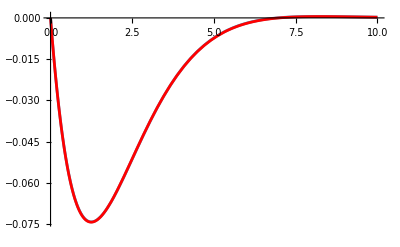

```mathematica
Show[ListLinePlot[q11Data],Plot[nlmq11[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
real11=(Mpstim[[4,4]]/.param/.paramScheme)/(nlmq11["ParameterTableEntries"][[2,1]])^2;
```

General::munfl: Exp[-862.018] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-743.777] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
mreal11=Solve[Mp[[4,4]]-real11==0,mO][[1,1,2]]/.param/.paramScheme
```

2867.43

```mathematica
nlmq21=NonlinearModelFit[q21Data,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf1'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
nlmq21["ParameterTable"]
```

General::munfl: Exp[-714.877] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.867189 | 0.000317561 | 2730.78 | 3.40991×10^-311
xi | 0.865424 | 0.000778244 | 1112.02 | 1.78995×10^-260

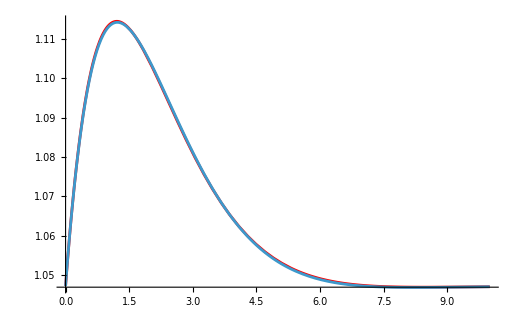

```mathematica
Show[Plot[nlmq21[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q21Data]]
```

```mathematica
real21=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq21["ParameterTableEntries"][[2,1]])^2;
```

General::munfl: Exp[-714.877] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
mreal21=Solve[Mp[[5,5]]-real21==0,mO][[1,1,2]]/.param/.paramScheme
```

2704.86

```mathematica
nlmq22=NonlinearModelFit[q22Data,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf2'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
nlmq22["ParameterTable"]
```

General::munfl: Exp[-761.063] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.840519 | 0.000338095 | 2486.04 | 0.
xi | 0.84084 | 0.000769492 | 1092.72 | 1.46402×10^-280

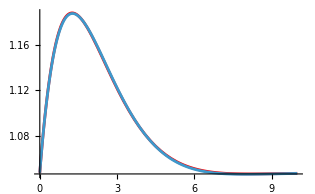

```mathematica
Show[Plot[nlmq22[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q22Data]]
```

```mathematica
real22=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq22["ParameterTableEntries"][[2,1]])^2;
```

General::munfl: Exp[-761.063] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
mreal22=Solve[Mp[[5,5]]-real22==0,mO][[1,1,2]]/.param/.paramScheme
```

2871.45

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal22}]
```

2786.14

2871.45

#### Nonlinearfit Symbolic Form with noise

```mathematica
w=WhiteNoiseProcess[0.005];
noiseData1=RandomFunction[w,{0,Dimensions[q11Data][[1]]-1}];
noiseData1y=Normal[noiseData1][[1,All,2]];
noiseData2=RandomFunction[w,{0,Dimensions[q22Data][[1]]-1}];
noiseData2y=Normal[noiseData2][[1,All,2]];
```

```mathematica
q11DataNoise=Transpose@{q11Data[[All,1]],q11Data[[All,2]]+noiseData1y};
q21DataNoise=Transpose@{q21Data[[All,1]],q21Data[[All,2]]+noiseData1y};
q12DataNoise=Transpose@{q12Data[[All,1]],q12Data[[All,2]]+noiseData2y};
q22DataNoise=Transpose@{q22Data[[All,1]],q22Data[[All,2]]+noiseData2y};
```

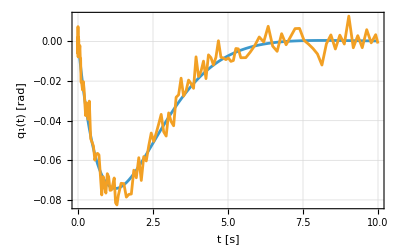

```mathematica
ListLinePlot[{q11Data,q11DataNoise},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618]
```

```mathematica
nlmq11Symb=NonlinearModelFit[q11DataNoise,q1[t]/.sol11,{{mO,499}},t]
nlmq11Symb["ParameterTable"]
real11Symbolic=nlmq11Symb["ParameterTableEntries"][[1,1]]
```

NonlinearModelFit::nrlnum: The function value {-0.00219374+0. ⅈ,0.00035151+0. ⅈ,-0.00753489+0. ⅈ,-0.00262626+0. ⅈ,0.00548542+0. ⅈ,0.00590959+0. ⅈ,0.0000350852+0. ⅈ,-0.00273051+0. ⅈ,0.00713242-3.27162×10^-17 ⅈ,«34»,0.00146968-8.17906×10^-18 ⅈ,0.00806576+0. ⅈ,0.00775232+0. ⅈ,0.00484076+0. ⅈ,0.00172296+0. ⅈ,0.0144484+0. ⅈ,0.0158206+0. ⅈ,«82»} is not a list of real numbers with dimensions {132} at {mO} = {2513.25}.

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2513.25 | 47.1734 | 53.2768 | 1.18432×10^-90

2513.25

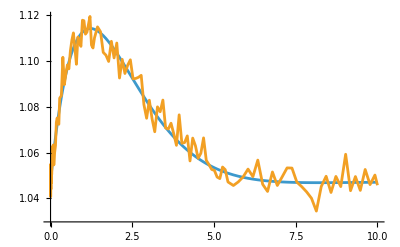

```mathematica
ListLinePlot[{q21Data,q21DataNoise}]
```

```mathematica
0.3*π/180
```

0.00523599

```mathematica
Plot[q2[t]/.sol21,{t,0,10}]
```

-Graphics-

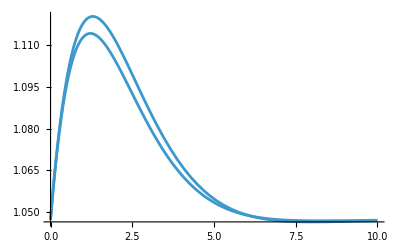

```mathematica
Show[Plot[q2[t]/.sol21/.mO->3000,{t,0,10},PlotRange->All],ListLinePlot[q21Data,PlotRange->All]]
```

```mathematica
nlmq21Symb=NonlinearModelFit[q21DataNoise,q2[t]/.sol21,{{mO,499}},t]
nlmq21Symb["ParameterTable"]
real21Symbolic=nlmq21Symb["ParameterTableEntries"][[1,1]]
```

NonlinearModelFit::nrlnum: The function value {-0.00219374+0. ⅈ,0.000351512+0. ⅈ,-0.00753489+0. ⅈ,-0.00262626+0. ⅈ,0.00548541+0. ⅈ,0.00590957+0. ⅈ,0.0000350022+0. ⅈ,-0.00273068+0. ⅈ,0.00713197+0. ⅈ,«33»,-0.0107681+0. ⅈ,-0.0102526+0. ⅈ,-0.00423665+0. ⅈ,-0.00510653+0. ⅈ,-0.0085493+0. ⅈ,-0.0121717+0. ⅈ,0.0000768137+0. ⅈ,0.00100076+0. ⅈ,«82»} is not a list of real numbers with dimensions {132} at {mO} = {2348.52}.

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2348.52 | 45.3788 | 51.7535 | 4.46142×10^-89

2348.52

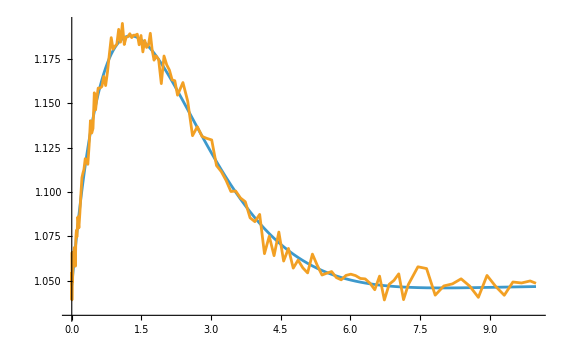

```mathematica
ListLinePlot[{q22Data,q22DataNoise}]
```

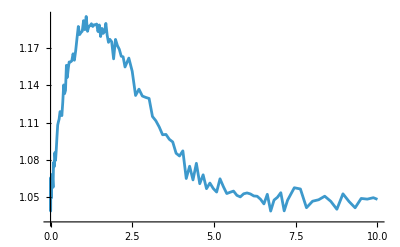

```mathematica
ListLinePlot[q22DataNoise]
```

```mathematica
nlmq12Symb=NonlinearModelFit[q12DataNoise,q1[t]/.sol12,{{mO,499}},t]
nlmq12Symb["ParameterTable"]
real12Symbolic=nlmq12Symb["ParameterTableEntries"][[1,1]]
```

NonlinearModelFit::nrjnum: The Jacobian is not a matrix of real numbers at {mO} = {2392.61}.

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2392.61 | 63.6018 | 37.6187 | 4.77297×10^-76

2392.61

```mathematica
nlmq22Symb=NonlinearModelFit[q22DataNoise,q2[t]/.sol22,{{mO,499}},t]
nlmq22Symb["ParameterTable"]
real22Symbolic=nlmq22Symb["ParameterTableEntries"][[1,1]]
```

NonlinearModelFit::nrlnum: The function value {-0.00575782+0. ⅈ,-0.00430562+0. ⅈ,-0.00554167+0. ⅈ,-0.00591905+0. ⅈ,-0.00329811+0. ⅈ,-0.00677298+0. ⅈ,-0.0027134+0. ⅈ,-0.00381761+0. ⅈ,0.00907169+0. ⅈ,«33»,-0.00591807+0. ⅈ,-0.00363248+0. ⅈ,-0.00652239+0. ⅈ,0.00112896+2.2061×10^-17 ⅈ,-0.00445386+0. ⅈ,-0.0124998+0. ⅈ,-0.0202583+0. ⅈ,-0.0123777+0. ⅈ,«94»} is not a list of real numbers with dimensions {144} at {mO} = {2442.27}.

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2442.27 | 39.524 | 61.7921 | 4.92961×10^-105

2442.27

```mathematica
Mean[{real11Symbolic,real21Symbolic}]
Mean[{real22Symbolic}]
```

2430.88

2442.27

#### Nonlinear Model Fit with noise

```mathematica
nlmq11=NonlinearModelFit[q11DataNoise,{(pf1'[[4]]/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t]},{{ω,0.8},{xi,0.8}},t];
```

```mathematica
nlmq11["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.857247 | 0.0067363 | 127.258 | 2.61498×10^-138
xi | 0.81232 | 0.0160353 | 50.6582 | 1.82616×10^-87

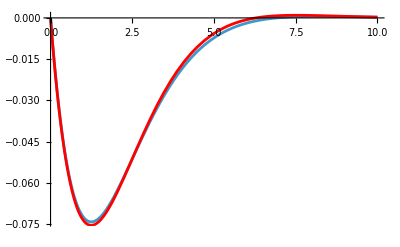

```mathematica
Show[ListLinePlot[q11Data],Plot[nlmq11[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
real11=(Mpstim[[4,4]]/.param/.paramScheme)/(nlmq11["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal11=Solve[Mp[[4,4]]-real11==0,mO][[1,1,2]]/.param/.paramScheme
```

3145.02

```mathematica
nlmq21=NonlinearModelFit[q21DataNoise,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf1'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.8}},t]
```

FittedModel[…]

```mathematica
nlmq21["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.856784 | 0.00788644 | 108.64 | 1.84008×10^-129
xi | 0.906811 | 0.0202558 | 44.768 | 7.3103×10^-81

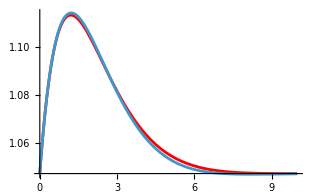

```mathematica
Show[Plot[nlmq21[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q21Data]]
```

```mathematica
real21=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq21["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal21=Solve[Mp[[5,5]]-real21==0,mO][[1,1,2]]/.param/.paramScheme
```

2454.42

```mathematica
nlmq12=NonlinearModelFit[q12DataNoise,(pf2'[[4]]/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t],{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
real12=(Mpstim[[4,4]]/.param/.paramScheme)/(nlmq12["ParameterTableEntries"][[1,1]])^2
```

278859.

```mathematica
mreal12=Solve[Mp[[4,4]]-real12==0,mO][[1,1,2]]/.param/.paramScheme
```

2817.36

```mathematica
nlmq22=NonlinearModelFit[q22DataNoise,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf2'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
nlmq22["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.8425 | 0.00397872 | 211.752 | 1.87592×10^-179
xi | 0.83295 | 0.00897667 | 92.7905 | 5.63764×10^-129

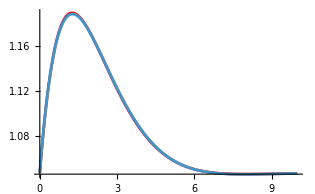

```mathematica
Show[Plot[nlmq22[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q22Data]]
```

```mathematica
real22=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq22["ParameterTableEntries"][[1,1]])^2;
```

```mathematica
mreal22=Solve[Mp[[5,5]]-real22==0,mO][[1,1,2]]/.param/.paramScheme
```

2859.73

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal12,mreal22}]
```

2799.72

2838.55

#### Parametric Plot Symbolic

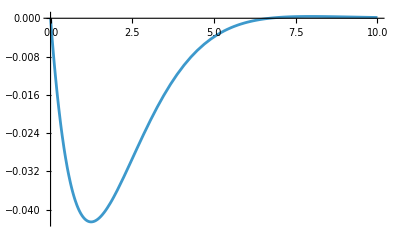

```mathematica
Plot[solMotionControl2[[4,2]],{t,0,10}]
```

```mathematica
{disp11,time11}=FindMinimum[solMotionControl1[[4,2]],{t,1,4}];
{disp21,time21}=FindMaximum[solMotionControl1[[5,2]],{t,1,2}];
{disp12,time12}=FindMaximum[solMotionControl2[[4,2]],{t,1,4}];
{disp22,time22}=FindMaximum[solMotionControl2[[5,2]],{t,1,4}];
```

InterpolatingFunction::dmval: Input value {-0.0397034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00389412} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000665195} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

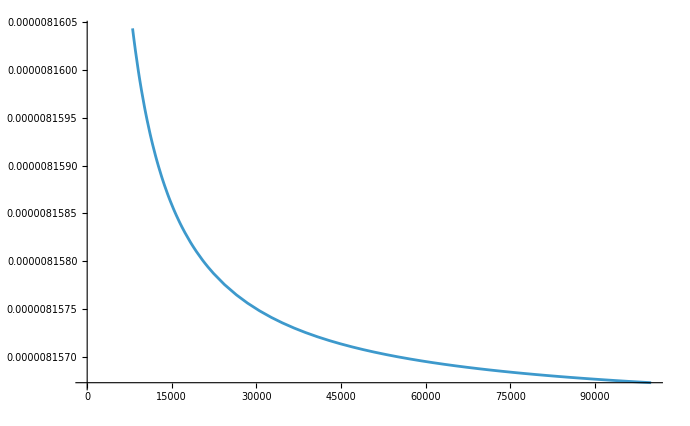

```mathematica
Plot[FullSimplify@(sol12[[1,2]]/.t->time12[[1,2]])-disp12,{mO,0,100000}]
```

```mathematica
mreal11=Re@FindRoot[FullSimplify@(sol11[[1,2]]/.t->time11[[1,2]])-disp11,{mO,1000,10000}][[1,2]]
mreal21=Re@FindRoot[FullSimplify@(sol21[[1,2]]/.t->time21[[1,2]])-disp21,{mO,2900,10000}][[1,2]]
mreal12=Re@FindRoot[FullSimplify@(sol12[[1,2]]/.t->time22[[1,2]])-disp12,{mO,1000,10000}][[1,2]]
mreal22=Re@FindRoot[FullSimplify@(sol22[[1,2]]/.t->time22[[1,2]])-disp22,{mO,2900,5000}][[1,2]]
```

2862.91

2684.25

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-214.111

2859.25

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal22}]
```

2773.58

2859.25

```mathematica
(1-Mean[{mreal11,mreal21}]/mO/.param)*100
(1-Mean[{mreal22}]/mO/.param)*100
```

7.54736

4.69157

#### Parametric Plot

```mathematica
D[(q0'/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t],t]//Simplify
FullSimplify[D[q0(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q0 Cos[ω Sqrt[1-xi^2] t]+(q0'+q0 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t],t]]
```

ⅇ^(-t xi ω) (Cos[t √(1-xi^2) ω]-(xi Sin[t √(1-xi^2) ω])/(√(1-xi^2))) q0'

ⅇ^(-t xi ω) (Cos[t √(1-xi^2) ω]-(xi Sin[t √(1-xi^2) ω])/(√(1-xi^2))) q0'

```mathematica
ωd=Simplify[Sqrt[1-mtest/m]Sqrt[mtest/m]];
β=Simplify[Sqrt[1-mtest/m]/Sqrt[mtest/m]];
```

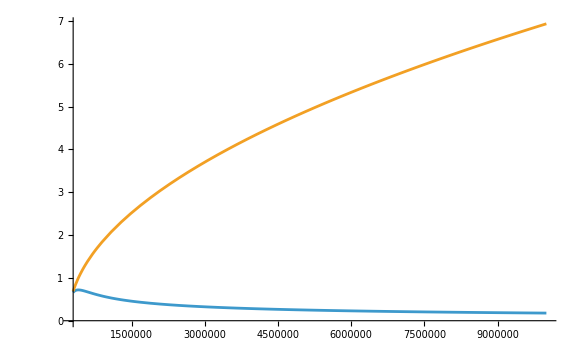

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time11[[1,2]]],β/.mtest->Mpstim[[4,4]]/.param/.paramScheme},{m,300000,10000000}]
```

```mathematica
real11=FindRoot[Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time11[[1,2]]]-β/.mtest->Mpstim[[4,4]]/.param/.paramScheme,{m,300000,370000}]
mreal11=Solve[Mp[[4,4]]-real11[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→284950.}

2883.74

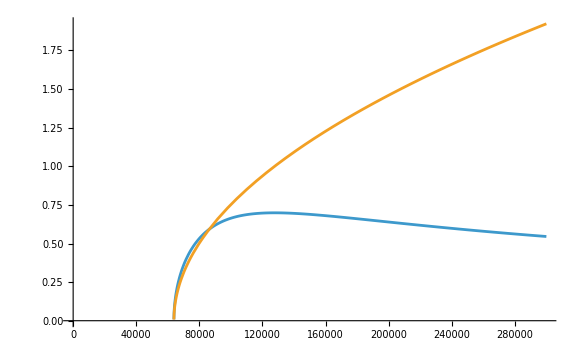

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time21[[1,2]]],β/.mtest->Mpstim[[5,5]]/.param/.paramScheme},{m,1,300000}]
```

```mathematica
real21=FindRoot[Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time21[[1,2]]]-β/.mtest->Mpstim[[5,5]]/.param/.paramScheme,{m,90000,100000}]
mreal21=Solve[Mp[[5,5]]-real21[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→86297.6}

2738.61

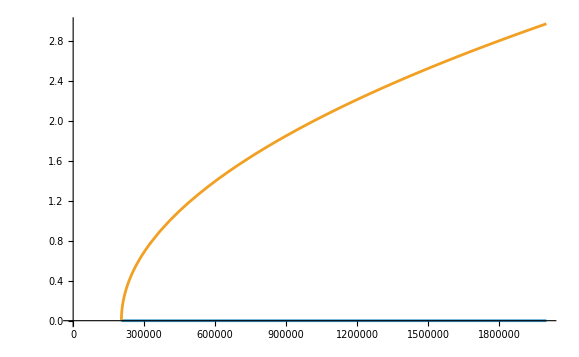

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time12[[1,2]]],β/.mtest->Mpstim[[4,4]]/.param/.paramScheme},{m,0,2000000}]
```

```mathematica
real12=FindRoot[Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time12[[1,2]]]-β/.mtest->Mpstim[[4,4]]/.param/.paramScheme,{m,400000,500000}]
mreal12=Solve[Mp[[4,4]]-real12[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→203850.-2.37712×10^-15 ⅈ}

2000.-2.59032×10^-17 ⅈ

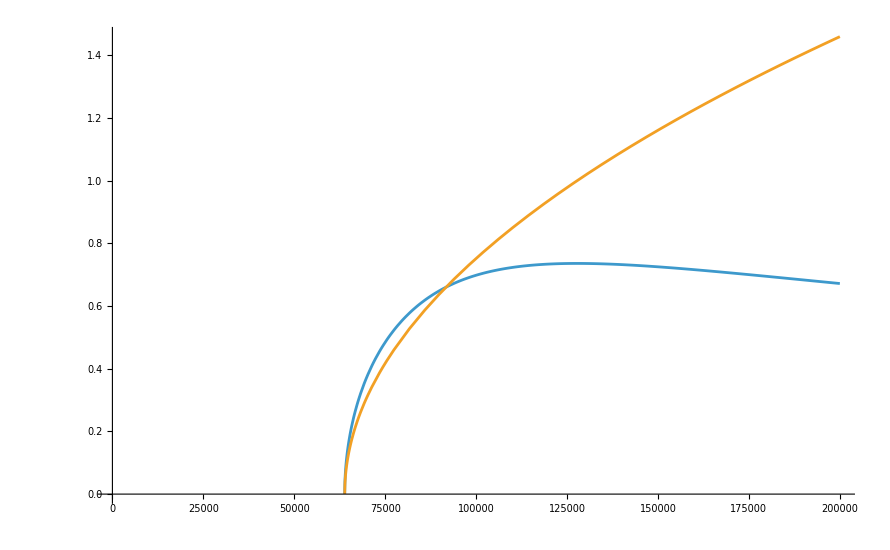

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time22[[1,2]]],β/.mtest->Mpstim[[5,5]]/.param/.paramScheme},{m,10,200000}]
```

```mathematica
real22=FindRoot[Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time22[[1,2]]]-β/.mtest->Mpstim[[5,5]]/.param/.paramScheme,{m,80000,100000}]
mreal22=Solve[Mp[[5,5]]-real22[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→91718.9}

2917.12

```mathematica
realmass1=Re@Mean[{mreal11,mreal21}]
realmass2=Re@Mean[{mreal22}]
```

2811.18

2917.12

```mathematica
(1-Mean[{mreal11,mreal21}]/mO/.param)*100
(1-Mean[{mreal22}]/mO/.param)*100
```

6.29414

2.76262

## Masses Plots

## Simulation 1

```mathematica
data10=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 1 - 0.csv"];
data1π6=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 1 - π 6.csv"];
data1π4=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 1 - π 4.csv"];
data1π3=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 1 - π 3.csv"];
data1π2=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 1 - π 2.csv"];
```

```mathematica
data1π3//MatrixForm
```

(500 | 1566. | 2330.19 | 1811.25 | 1888.3
1000 | 2217.88 | 2421.31 | 2321.95 | 2384.79
1500 | 2545.02 | 2627.13 | 2591.81 | 2649.06
2000 | 2763.03 | 2786.46 | 2773.58 | 2811.18
2500 | 2901.93 | 2906.31 | 2901.26 | 2920.74
3000 | 2999.28 | 3000.39 | 2999.93 | 3000.
3500 | 3070.48 | 3072.34 | 3073.46 | 3060.26
4000 | 3128.01 | 3134.63 | 3133.47 | 3107.85
4500 | 3175.89 | 3186.9 | 3182.96 | 3146.58
5000 | 3216.63 | 3232.84 | 3224.63 | 3178.89)

```mathematica
masses=data10[[1;;10,1]]
```

{500,1000,1500,2000,2500,3000,3500,4000,4500,5000}

```mathematica
fitMo10=Transpose[{masses,data10[[1;;10,2]]}];
fitxiomega10=Transpose[{masses,data10[[1;;10,3]]}];
positionRoots10=Transpose[{masses,data10[[1;;10,4]]}];
derivativeRoots10=Transpose[{masses,data10[[1;;10,5]]}];
fitMo1π6=Transpose[{masses,data1π6[[1;;10,2]]}];
fitxiomega1π6=Transpose[{masses,data1π6[[1;;10,3]]}];
positionRoots1π6=Transpose[{masses,data1π6[[1;;10,4]]}];
derivativeRoots1π6=Transpose[{masses,data1π6[[1;;10,5]]}];
fitMo1π4=Transpose[{masses,data1π4[[1;;10,2]]}];
fitxiomega1π4=Transpose[{masses,data1π4[[1;;10,3]]}];
positionRoots1π4=Transpose[{masses,data1π4[[1;;10,4]]}];
derivativeRoots1π4=Transpose[{masses,data1π4[[1;;10,5]]}];
fitMo1π3=Transpose[{masses,data1π3[[1;;10,2]]}];
fitxiomega1π3=Transpose[{masses,data1π3[[1;;10,3]]}];
positionRoots1π3=Transpose[{masses,data1π3[[1;;10,4]]}];
derivativeRoots1π3=Transpose[{masses,data1π3[[1;;10,5]]}];
fitMo1π2=Transpose[{masses,data1π2[[2;;11,3]]}];
fitxiomega1π2=Transpose[{masses,data1π2[[2;;11,5]]}];
positionRoots1π2=Transpose[{masses,data1π2[[2;;11,6]]}];
derivativeRoots1π2=Transpose[{masses,data1π2[[2;;11,7]]}];
```

```mathematica
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{1600,3800}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo10,fitxiomega10,positionRoots10,derivativeRoots10},PlotRange->{Automatic,{1600,3800}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = 0",Black]]
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{800,3900}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo1π6,fitxiomega1π6,positionRoots1π6,derivativeRoots1π6},PlotRange->{Automatic,{800,3900}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/6",Black]]
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{1200,3800}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo1π4,fitxiomega1π4,positionRoots1π4,derivativeRoots1π4},PlotRange->{Automatic,{1200,3800}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/4",Black]]
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{1500,3500}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo1π3,fitxiomega1π3,positionRoots1π3,derivativeRoots1π3},PlotRange->{Automatic,{1500,3500}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/3",Black]]
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{1600,3300}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo1π2,fitxiomega1π2,positionRoots1π2,derivativeRoots1π2},PlotRange->{Automatic,{1600,3300}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/2",Black]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

## Simulation 2

```mathematica
data2π6=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 2 - π 6.csv"];
data2π4=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 2 - π 4.csv"];
data2π3=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 2 - π 3.csv"];
data2π2=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Masses_Evaluation/Simulation 2 - π 2.csv"];
```

```mathematica
data2π3//MatrixForm
```

(500 | 1776.86 | 2158.93 | 2246.98 | 2112.
1000 | 2630.04 | 2618.72 | 2571.18 | 2508.19
1500 | 2679.97 | 2784.6 | 2746.57 | 2719.19
2000 | 2787.97 | 2813.27 | 2810.18 | 2458.56
2500 | 2922.22 | 2926.6 | 2917.21 | 2732.04
3000 | 2994.55 | 2995.89 | 3012.76 | 3000.
3500 | 3055.62 | 3082.12 | 3062.9 | 3048.59
4000 | 3098.17 | 3105.37 | 3114.95 | 3087.15
4500 | 3146.21 | 3128.93 | 3158.24 | 3118.69
5000 | 3179.55 | 3204.2 | 3194.95 | 3145.13)

```mathematica
fitMo2π6=Transpose[{masses,data2π6[[1;;10,2]]}];
fitxiomega2π6=Transpose[{masses,data2π6[[1;;10,3]]}];
positionRoots2π6=Transpose[{masses,data2π6[[1;;10,4]]}];
derivativeRoots2π6=Transpose[{masses,data2π6[[1;;10,5]]}];
fitMo2π4=Transpose[{masses,data2π4[[1;;10,2]]}];
fitxiomega2π4=Transpose[{masses,data2π4[[1;;10,3]]}];
positionRoots2π4=Transpose[{masses,data2π4[[1;;10,4]]}];
derivativeRoots2π4=Transpose[{masses,data2π4[[1;;10,5]]}];
fitMo2π3=Transpose[{masses,data2π3[[1;;10,2]]}];
fitxiomega2π3=Transpose[{masses,data2π3[[1;;10,3]]}];
positionRoots2π3=Transpose[{masses,data2π3[[1;;10,4]]}];
derivativeRoots2π3=Transpose[{masses,data2π3[[1;;10,5]]}];
fitMo2π2=Transpose[{masses,data2π2[[2;;11,3]]}];
fitxiomega2π2=Transpose[{masses,data2π2[[2;;11,5]]}];
positionRoots2π2=Transpose[{masses,data2π2[[2;;11,6]]}];
derivativeRoots2π2=Transpose[{masses,data2π2[[2;;11,7]]}];
```

```mathematica
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{800,3900}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo2π6,fitxiomega2π6,positionRoots2π6,derivativeRoots2π6},PlotRange->{Automatic,{800,3900}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/6",Black]]
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{1200,3800}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo2π4,fitxiomega2π4,positionRoots2π4,derivativeRoots2π4},PlotRange->{Automatic,{1200,3800}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/4",Black]]
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{1500,3500}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo2π3,fitxiomega2π3,positionRoots2π3,derivativeRoots2π3},PlotRange->{Automatic,{1500,3500}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/3",Black]]
Show[Plot[3000,{x,0,5000},PlotStyle->{Red,Dashed},PlotRange->{Automatic,{1900,3300}},Frame->True,Axes->False,FrameLabel->{"OverHat[m_O] [kg]","m_O [kg]"},ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",20],Background->White,AspectRatio->1/1.618,FrameTicks->{masses,Automatic}],ListLinePlot[{fitMo2π2,fitxiomega2π2,positionRoots2π2,derivativeRoots2π2},PlotRange->{Automatic,{1900,3300}},LabelStyle->Directive[FontFamily->"Source Serif Pro",20],PlotLegends->Placed[LineLegend[{Row[{"m_O Fit"}],Row[{"ξ, ω Fit"}],Row[{"Position Roots"}],Row[{"Derivative Roots"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large]],PlotLabel->Style["q_(2, 0) = π/2",Black]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## Kinetic Parameters Extraction

```mathematica
data1π6//MatrixForm
```

(500 | 1166.44 | 902.01 | 828.64 | 871.4
1000 | 1174.35 | 1223.16 | 1388.56 | 1312.35
1500 | 1904.87 | 2642.39 | 1875.71 | 1941.28
2000 | 2310.89 | 2435.61 | 2309.34 | 2329.92
2500 | 2684.62 | 2706.62 | 2685.31 | 2710.88
3000 | 3011.92 | 3008.02 | 3049.67 | 3000.
3500 | 3235.42 | 3274.16 | 3260.69 | 3213.13
4000 | 3398.1 | 3475.78 | 3480.89 | 3373.87
4500 | 3543.7 | 3725.6 | 3668.14 | 3498.74
5000 | 3651.29 | 3871.59 | 3829.2 | 3598.39)

```mathematica
realmass1=Mean[{data1π6[[10,2]],data1π6[[10,3]],data1π6[[10,4]],data1π6[[10,5]]}]
realmass2=Mean[{data2π6[[10,2]],data2π6[[10,3]],data2π6[[10,4]],data2π6[[10,5]]}]
```

3737.62

3425.68

```mathematica
initialConditionsSymbolic={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0};
```

Initial object’s velocities without knowing Ω’[t]:

```mathematica
solVel1=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[2]]]==ψf1'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[3]]]==ψf1'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
solVel2=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[2]]]==ψf2'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[3]]]==ψf2'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
```

yO'[t]==-1.68445+1.73205 xO'[t]&&Ω'[t]==2261.72-2314.81 xO'[t]

yO'[t]==-0.98504+1.73205 xO'[t]&&Ω'[t]==-11.4513-2314.81 xO'[t]

Initial object' s velocities knowing Ω'[t] :

```mathematica
solVel1Acc=Chop[Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf1'[[2]]},{xO'[t],yO'[t],Ω'[t]}],10^-4]
solVel2Acc=Chop[Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf2'[[2]]},{xO'[t],yO'[t],Ω'[t]}],10^-4]
```

xO'[t]==0.977065&&yO'[t]==0.00787112

xO'[t]==-0.00494696&&yO'[t]==-0.993609

```mathematica
momentumEq1=Chop@Simplify[M.(p'/.{p'[[1]]->pf1'[[1]],p'[[2]]->pf1'[[2]],p'[[3]]->pf1'[[3]],p'[[4]]->pf1'[[4]],p'[[5]]->pf1'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf1'[[1]],yO'[t]->ψf1'[[2]],Ω'[t]->ψf1'[[3]]})-({xO'[t],yO'[t],Ω'[t]}))/.paramExtraction/.mO->realmass1/.paramScheme/.Ω'[t]->0]
Solve[{momentumEq1[[1]]==0,momentumEq1[[2]]==0},{xO'[t],yO'[t]}][[1]]
```

{3638.75-3724.35 xO'[t]+22.9746 yO'[t],6.66046+22.9746 xO'[t]-3697.82 yO'[t],-30543.2+31117.5 xO'[t]+17708.8 yO'[t],-30543.2+31117.5 xO'[t]+17708.8 yO'[t],-10202.6+10298.3 xO'[t]+17837.3 yO'[t]}

{xO'[t]→0.977065,yO'[t]→0.0078717}

```mathematica
momentumEq2=Chop@Simplify[M.(p'/.{p'[[1]]->pf2'[[1]],p'[[2]]->pf2'[[2]],p'[[3]]->pf2'[[3]],p'[[4]]->pf2'[[4]],p'[[5]]->pf2'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf2'[[1]],yO'[t]->ψf2'[[2]],Ω'[t]->ψf2'[[3]]})-({xO'[t],yO'[t],Ω'[t]}))/.paramExtraction/.mO->realmass2/.paramScheme/.Ω'[t]->0]
sol2=Solve[{momentumEq2[[1]]==0,momentumEq2[[2]]==0},{xO'[t],yO'[t]}][[1]]
```

{4.03412-3413.52 xO'[t]+21.0572 yO'[t],-3367.44+21.0572 xO'[t]-3389.21 yO'[t],16268.2+28520.4 xO'[t]+16230.9 yO'[t],16268.2+28520.4 xO'[t]+16230.9 yO'[t],16290.8+9438.85 xO'[t]+16348.6 yO'[t]}

{xO'[t]→-0.00494753,yO'[t]→-0.993609}

## Plots

```mathematica
velocity1π2=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Velocities/Simulation 1 - π 2.csv"];
velocity1π6=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Velocities/Simulation 1 - π 6.csv"];
velocity2π2=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Velocities/Simulation 2 - π 2.csv"];
velocity2π6=Import["/Users/simonemanfredi/Desktop/Uni/Magistrale/Tesi/Master-Thesis/Mathematica/Velocities/Simulation 2 - π 6.csv"];
```

```mathematica
velocity2π2//MatrixForm
```

(Mass | Vx | Vy | Ex | Ey
500 | 0 | -1.006 | 0 | 0.6
1000 | 0 | -1.0029 | 0 | 0.29
1500 | 0 | -1.0013 | 0 | 0.13
2000 | 0 | -1.00058 | 0 | 0.058
2500 | 0 | -1.00031 | 0 | 0.031
3000 | 0 | -0.9999 | 0 | 0.01
3500 | 0 | -0.9998 | 0 | 0.02
4000 | 0 | -0.9997 | 0 | 0.03
4500 | 0 | -0.9995 | 0 | 0.05
5000 | 0 | -0.9992 | 0 | 0.08)

```mathematica
vel1π2x=Transpose[{masses,velocity1π2[[2;;11,4]]}];
vel1π2y=Transpose[{masses,velocity1π2[[2;;11,5]]}];
vel1π6x=Transpose[{masses,velocity1π6[[2;;11,4]]}];
vel1π6y=Transpose[{masses,velocity1π6[[2;;11,5]]}];
vel2π2x=Transpose[{masses,velocity2π2[[2;;11,4]]}];
vel2π2y=Transpose[{masses,velocity2π2[[2;;11,5]]}];
vel2π6x=Transpose[{masses,velocity2π6[[2;;11,4]]}];
vel2π6y=Transpose[{masses,velocity2π6[[2;;11,5]]}];
```

### Simulation 1

```mathematica
ListLinePlot[{vel1π2x,vel1π2y},PlotRange->{Automatic,{-1,4.5}},LabelStyle->Directive[FontFamily->"Source Serif Pro",16],PlotLegends->Placed[LineLegend[{Row[{"err_x"}],Row[{"err_y"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large],Frame->True,ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/1.618,FrameTicks->{masses,Automatic},FrameLabel->{"OverTilde[m_O] [kg]","e_%"},PlotLabel->Style["q_(2, 0) = π/2",Black]]
ListLinePlot[{vel1π6x,vel1π6y},PlotRange->{Automatic,{-1,25}},LabelStyle->Directive[FontFamily->"Source Serif Pro",16],PlotLegends->Placed[LineLegend[{Row[{"err_x"}],Row[{"err_y"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large],Frame->True,ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/1.618,FrameTicks->{masses,Automatic},FrameLabel->{"OverTilde[m_O] [kg]","e_%"},PlotLabel->Style["q_(2, 0) = π/6",Black]]
```

-Graphics-

-Graphics-

### Simulation 2

```mathematica
ListLinePlot[{vel2π2x,vel2π2y},PlotRange->{Automatic,{-0.1,0.8}},LabelStyle->Directive[FontFamily->"Source Serif Pro",16],PlotLegends->Placed[LineLegend[{Row[{"err_x"}],Row[{"err_y"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large],Frame->True,ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/1.618,FrameTicks->{masses,Automatic},FrameLabel->{"OverTilde[m_O] [kg]","e_%"},PlotLabel->Style["q_(2, 0) = π/2",Black]]
ListLinePlot[{vel2π6x,vel2π6y},PlotRange->{Automatic,{-1,20}},LabelStyle->Directive[FontFamily->"Source Serif Pro",16],PlotLegends->Placed[LineLegend[{Row[{"err_x"}],Row[{"err_y"}]}],{1,0.5}],Mesh->Full,MeshStyle->Directive[PointSize->Large],Frame->True,ImageSize->Full,FrameStyle->Directive[Black],GridLines->All,GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/1.618,FrameTicks->{masses,Automatic},FrameLabel->{"OverTilde[m_O] [kg]","e_%"},PlotLabel->Style["q_(2, 0) = π/6",Black]]
```

-Graphics-

-Graphics-